```mathematica
SIR[a_,r_,s0_,i0_,r0_,t_,n_]:=(
x=Table[0,t+1];
x[[1]]=s0;
y=Table[0,t+1];
y[[1]]=i0;
z=Table[0,t+1];
z[[1]]=r0;
h=t/n;
For[i=1,i<t+1,i++,
x[[i+1]]=x[[i]] (1-h r y[[i]]);
y[[i+1]]=y[[i]] (1+h (r x[[i]]-a));
z[[i+1]]=z[[i]]+a h y[[i]];];
{x,y,z})
```

1

```mathematica
result1=SIR[0.73,0.0178,225,15,0,100,1000]
```

{{225,218.993,211.23,201.372,189.125,174.341,157.119,137.914,117.574,97.2417,78.1341,61.2444,47.1309,35.8785,27.2194,20.7101,15.879,12.3088,9.66504,7.69521,6.21436,5.0894,4.22515,3.55354,3.02567,2.60618,2.26929,1.99599,1.77219,1.58728,1.43323,1.30389,1.19452,1.1014,1.02162,0.952884,0.893333,0.841485,0.796133,0.756294,0.721157,0.690053,0.662426,0.637808,0.615807,0.596092,0.57838,0.562431,0.548037,0.535022,0.523231,0.512531,0.502805,0.493951,0.485881,0.478515,0.471783,0.465626,0.459987,0.454818,0.450077,0.445724,0.441724,0.438046,0.434662,0.431547,0.428677,0.426033,0.423594,0.421345,0.419269,0.417353,0.415583,0.413948,0.412438,0.411041,0.40975,0.408556,0.407452,0.40643,0.405484,0.404609,0.403798,0.403048,0.402353,0.40171,0.401114,0.400562,0.400051,0.399577,0.399138,0.398731,0.398354,0.398004,0.39768,0.39738,0.397102,0.396844,0.396604,0.396383,0.396177},{15,19.9125,26.2209,34.1656,43.9179,55.4965,68.6673,82.8589,97.151,110.391,121.44,129.464,134.127,135.588,134.349,131.051,126.315,120.665,114.5,108.111,101.7,95.4008,89.3008,83.4535,77.8892,72.6228,67.6582,62.9925,58.6178,54.5236,50.6975,47.1259,43.7951,40.6912,37.8005,35.1098,32.6063,30.2779,28.113,26.1006,24.2304,22.4926,20.8783,19.3788,17.9862,16.6929,15.492,14.377,13.3419,12.381,11.489,10.661,9.89243,9.17914,8.51713,7.90275,7.33258,6.80346,6.31245,5.85681,5.434,5.04167,4.67763,4.33984,4.02642,3.7356,3.46577,3.21542,2.98313,2.76761,2.56765,2.38213,2.21,2.05031,1.90215,1.76469,1.63715,1.51884,1.40907,1.30723,1.21274,1.12509,1.04377,0.968323,0.89833,0.833395,0.773153,0.717265,0.665416,0.617315,0.57269,0.53129,0.492883,0.457252,0.424197,0.393531,0.365081,0.338688,0.314203,0.291488,0.270415},{0,1.095,2.54861,4.46274,6.95683,10.1628,14.2141,19.2268,25.2755,32.3675,40.426,49.2911,58.742,68.5333,78.4313,88.2388,97.8055,107.027,115.835,124.194,132.086,139.51,146.474,152.993,159.085,164.771,170.072,175.012,179.61,183.889,187.869,191.57,195.01,198.207,201.178,203.937,206.5,208.881,211.091,213.143,215.048,216.817,218.459,219.983,221.398,222.711,223.93,225.061,226.11,227.084,227.988,228.827,229.605,230.327,230.997,231.619,232.196,232.731,233.228,233.688,234.116,234.513,234.881,235.222,235.539,235.833,236.106,236.359,236.593,236.811,237.013,237.201,237.374,237.536,237.685,237.824,237.953,238.073,238.183,238.286,238.382,238.47,238.552,238.629,238.699,238.765,238.826,238.882,238.935,238.983,239.028,239.07,239.109,239.145,239.178,239.209,239.238,239.264,239.289,239.312,239.333}}

```mathematica
Dimensions[result1]
```

{3,101}

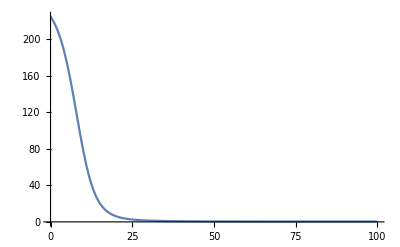

```mathematica
ListLinePlot[Table[{i-1,result1[[1]][[i]]},{i,1,Length[result1[[1]]]}],PlotRange->All]
```

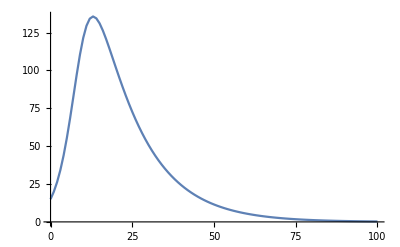
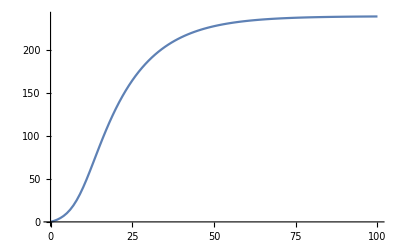
GraphicsRow[-Graphics-,-Graphics-,-Graphics-]

```mathematica
GraphicsRow[ListLinePlot[Table[{i-1,result1[[1]][[i]]},{i,1,Length[result1[[1]]]}],PlotRange->All],ListLinePlot[Table[{i-1,result1[[2]][[i]]},{i,1,Length[result1[[2]]]}],PlotRange->All],ListLinePlot[Table[{i-1,result1[[3]][[i]]},{i,1,Length[result1[[3]]]}],PlotRange->All]]
```